```mathematica
SetDirectory["/Users/brucesawhill/Desktop/SATSAir"]
FileNames[]
```

/Users/brucesawhill/Desktop/SATSAir

{cumulativetraffic2data,CumulativeTraffic2FullPlot.jpg,CumulativeTraffic2.jpg,Cumulative_Traffic_Detail.jpg,CumulativeTraffic.jpg,.DS_Store,Linear_PopularityPlot.jpg,OD_Pair_Popularity.jpg,PopularityPlot.jpg,RevenueFlightDurations.jpg,SATSAir_Analysis.nb,satsair_flights_data_pull_Sept_14_2009.rar,satsair_flights_data_pull_Sept_14_2009.xls,SATSdata-csv-10.05.28,SATS_Data_Tour.ppt,SATS_Data_Tour-v1.1.ppt,SATS_Data_Tour-v1.2.ppt,SATS_Data_Tour-v1.3.ppt,SATS_Flights.csv}

```mathematica
flightdata=Import["SATS_Flights.csv","CSV"];
```

```mathematica
Dimensions[flightdata]
```

{48710,25}

```mathematica
flightdata[[1]]
```

{l_my_leg_id,l_my_trip_id,l_trip_num,l_leg_seq_num,l_leg_cust_id,l_pilot_1_id,l_plane_id,l_plane,l_depart,l_arrive,l_time_out,l_time_off,l_time_on,l_time_in,l_charter,l_hobbs_start,l_hobbs_end,l_hobbs_billed,l_flight_start,l_flight_end,l_flight_tot,l_billed,l_passenger_1_weight,l_passenger_2_weight,l_passenger_3_weight}

```mathematica
slkjdf=Union[Table[flightdata[[i,15]],{i,2,Length[flightdata]}]]
```

{,BLOCK,BUS_DEV,CHARTER,DEAD_LEG,MAINT,RETAIL,TRAINING}

```mathematica
revflights=DeleteCases[Table[If[flightdata[[i,15]]=="BUS_DEV"||flightdata[[i,15]]=="MAINT"||flightdata[[i,15]]=="TRAINING"||flightdata[[i,15]]==""
||flightdata[[i,15]]=="DEAD_LEG",0,flightdata[[i]]],{i,2,Length[flightdata]}],0];
```

```mathematica
Dimensions[revflights]
```

{23331,25}

```mathematica
cities=Flatten[Table[Take[revflights[[i]],{9,10}],{i,2,Length[revflights]}]];
```

```mathematica
citypairs=Table[Take[revflights[[i]],{9,10}],{i,2,Length[revflights]}];
```

```mathematica
citypopularity=Sort[Tally[cities],#2[[2]]<#1[[2]]&];
```

```mathematica
citypopularity[[1]]
```

{GMU,3999}

```mathematica
citypairspopularity=Sort[Tally[citypairs],#2[[2]]<#1[[2]]&];
```

```mathematica
citypairspopularity>>rankedcitypairs;
```

```mathematica
Take[citypairspopularity,10]
```

{{{CHS,GMU},179},{{GMU,CHS},176},{{GMU,MCN},136},{{MCN,GMU},133},{{PDK,SSI},98},{{GMU,GGE},97},{{GMU,MYR},93},{{GGE,GMU},90},{{MYR,GMU},85},{{PDK,CAE},78}}

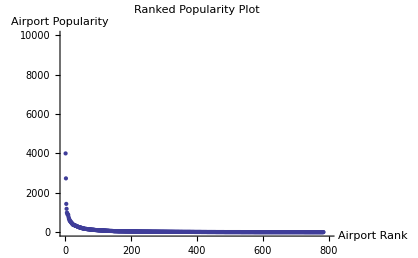

```mathematica
ListPlot[Table[{i,citypopularity[[i,2]]},{i,Length[citypopularity]}],PlotRange->{{0,800},{0,10000}},AxesLabel->{"Airport Rank","Airport Popularity"},PlotLabel->"Ranked Popularity Plot"]
```

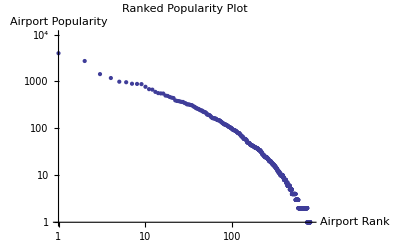

```mathematica
ListLogLogPlot[Table[{i,citypopularity[[i,2]]},{i,Length[citypopularity]}],PlotRange->{{1,800},{1,10000}},AxesLabel->{"Airport Rank","Airport Popularity"},PlotLabel->"Ranked Popularity Plot"]
```

```mathematica
Length[citypopularity]
```

784

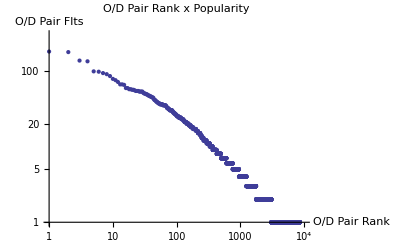

```mathematica
ListLogLogPlot[Table[{i,citypairspopularity[[i,2]]},{i,8486}],PlotRange->{{1,10000},{1,300}},AxesLabel->{"O/D Pair Rank","O/D Pair Flts"},PlotLabel->"O/D Pair Rank x Popularity"]
```

```mathematica
Length[cities]
```

46660

```mathematica
revflights[[1]]
```

{208,134,124,2,10097,17,9,N602CD,BHM,GMU,2005-11-16 17:25:00,2005-11-16 17:50:00,2005-11-16 19:02:00,2005-11-16 19:04:00,RETAIL,446.2,447.8,1.6,no_data,no_data,72,Y,no_data,no_data,no_data}

```mathematica
Length[revflights]
```

23331

```mathematica
revflights[[11,21]]
```

20

```mathematica
a=0
Do[If[revflights[[i,21]]=="no_data",a++],{i,Length[revflights]}]
a
```

0

12

```mathematica
2457/(23331-23)//N
```

0.105414

```mathematica
1849514/(23331-23)//N
```

79.351

```mathematica
Min[Table[revflights[[i,21]],{i,Length[revflights]}]]
```

Min[-1370,no_data]

```mathematica
Needs[Histogram]
```

```mathematica
timeplot=Histogram[Table[revflights[[i,21]],{i,Length[revflights]}],{0,250,6},PlotRange->{{0,250},{0,2100}},AxesLabel->{"Flight Time (min)","No. Flts."},PlotLabel->"Revenue Flights"]
```

-Graphics-

```mathematica
citypairspopularity[[4]]
```

{{MCN,GMU},133}

```mathematica
cumpts=Table[{Length[Union[Flatten[Table[Flatten[citypairspopularity[[i,1]]],{i,m}]]]],Sum[citypairspopularity[[i,2]]/23331.,{i,m}]},{m,200}];
```

```mathematica
ListPlot[cumpts,AxesLabel->{"No. Airports Served", "Traffic Fraction"},PlotLabel->"Cumulative Traffic Plot"]
```

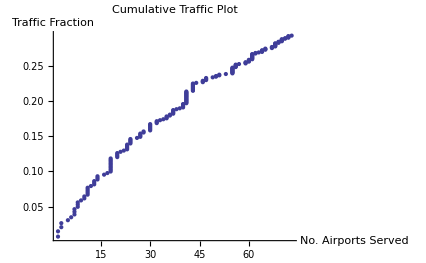

```mathematica
citypopularity[[2]]
```

{PDK,2731}

```mathematica
permpairs[p_]:=DeleteCases[Flatten[Table[If[i==j,0,{citypopularity[[i,1]],citypopularity[[j,1]]}],{i,p},{j,p}],1],0]
```

```mathematica
prs=permpairs[9]
```

{{GMU,PDK},{GMU,CHS},{GMU,RDU},{GMU,MYR},{GMU,SPA},{GMU,HXD},{GMU,AVL},{GMU,CLT},{PDK,GMU},{PDK,CHS},{PDK,RDU},{PDK,MYR},{PDK,SPA},{PDK,HXD},{PDK,AVL},{PDK,CLT},{CHS,GMU},{CHS,PDK},{CHS,RDU},{CHS,MYR},{CHS,SPA},{CHS,HXD},{CHS,AVL},{CHS,CLT},{RDU,GMU},{RDU,PDK},{RDU,CHS},{RDU,MYR},{RDU,SPA},{RDU,HXD},{RDU,AVL},{RDU,CLT},{MYR,GMU},{MYR,PDK},{MYR,CHS},{MYR,RDU},{MYR,SPA},{MYR,HXD},{MYR,AVL},{MYR,CLT},{SPA,GMU},{SPA,PDK},{SPA,CHS},{SPA,RDU},{SPA,MYR},{SPA,HXD},{SPA,AVL},{SPA,CLT},{HXD,GMU},{HXD,PDK},{HXD,CHS},{HXD,RDU},{HXD,MYR},{HXD,SPA},{HXD,AVL},{HXD,CLT},{AVL,GMU},{AVL,PDK},{AVL,CHS},{AVL,RDU},{AVL,MYR},{AVL,SPA},{AVL,HXD},{AVL,CLT},{CLT,GMU},{CLT,PDK},{CLT,CHS},{CLT,RDU},{CLT,MYR},{CLT,SPA},{CLT,HXD},{CLT,AVL}}

```mathematica
inds=DeleteCases[Table[If[Position[citypairspopularity,prs[[i]]]=={},0,Position[citypairspopularity,prs[[i]]][[1,1]]],{i,Length[prs]}],0]
```

{19,2,22,7,2285,25,550,198,18,32,230,68,137,55,164,14,1,23,26,1674,114,1185,228,54,31,255,35,327,201,229,124,52,9,91,361,326,49,122,356,353,1220,225,126,199,29,116,39,62,1186,190,140,100,288,3478,282,233,311,171,224,258,528,178,17,38,71,221,1415,1088}

```mathematica
pops=Sum[citypairspopularity[[inds[[j]],2]],{j,Length[inds]}]
```

2124

```mathematica
poptable=Table[0,{i,41}];
k=1;
Do[
{
prs=permpairs[j];
inds=DeleteCases[Table[If[Position[citypairspopularity,prs[[i]]]=={},0,Position[citypairspopularity,prs[[i]]][[1,1]]],{i,Length[prs]}],0];
poptable[[k]]={j,Sum[citypairspopularity[[inds[[t]],2]]/23330.,{t,Length[inds]}]};
Print[j];
k++
},{j,10,784,20}
]
```

10

30

50

70

90

110

130

150

170

190

210

230

250

270

290

310

330

350

370

390

410

430

450

470

490

510

530

550

570

590

610

630

650

670

690

710

$Aborted

```mathematica
MemoryInUse[]
```

100797672

```mathematica
poptable
```

{{10,0.104672},{30,0.294299},{50,0.421217},{70,0.505015},{90,0.575739},{110,0.635619},{130,0.688213},{150,0.728676},{170,0.763223},{190,0.792799},{210,0.820917},{230,0.842435},{250,0.861595},{270,0.878654},{290,0.893656},{310,0.906258},{330,0.917531},{350,0.927004},{370,0.935405},{390,0.943078},{410,0.949807},{430,0.955765},{450,0.960609},{470,0.964938},{490,0.968581},{510,0.971796},{530,0.975096},{550,0.977754},{570,0.980326},{590,0.982126},{610,0.983841},{630,0.985255},{650,0.986841},{670,0.988513},{690,0.990227},{710,0.991942},0,0,0,0,0}

```mathematica
FileNames[]
```

{cumulativetraffic2data,CumulativeTraffic2FullPlot.jpg,CumulativeTraffic2.jpg,Cumulative_Traffic_Detail.jpg,CumulativeTraffic.jpg,.DS_Store,Linear_PopularityPlot.jpg,OD_Pair_Popularity.jpg,PopularityPlot.jpg,RevenueFlightDurations.jpg,SATSAir_Analysis.nb,SATS_Data_Tour.ppt,SATS_Flights.csv}

```mathematica
poptable>>cumulativetraffic2data;
```

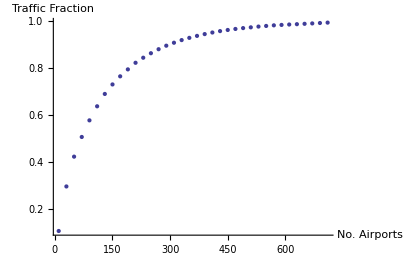

```mathematica
ListPlot[Take[poptable,36],AxesLabel->{"No. Airports", "Traffic Fraction"}]
```

```mathematica
Table[{i,pops[i]},{i,10}]
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part will be suppressed during this calculation.

$Aborted

```mathematica
indices[3]
```

{19,2,18,32,1,23}

```mathematica
indices[[1]]
```

Part::partd: Part specification indices ⟦ 1 ⟧ is longer than depth of object.

indices⟦1⟧

```mathematica
citypairspopularity[[1,2]]
```

179